```mathematica
Zangle[U_] := ArcTan[Re[U[[2, 2]]/U[[1, 1]]], Im[U[[2, 2]]/U[[1, 1]]]]
```

```mathematica
setVariables[];

Eamp[t_] := 0;
Bamp[t_] := 0;

ΔE = 10000;
UbaseLab = MatrixExp[-ⅈ*t*(HexactStatic /. t->0) // N];

ZfidelityWithNoise[T_?NumericQ, ϕTarget_, δE_] := (
statusString = "Error of " <> ToString[δE] <> "V/m          ";
Tmax = T;
T1 = Min[5*10^-9, Tmax/2];
T2 = Tmax - 2*T1;
ΔΔE = 20000*Min[1, T1/(5*10^-9)];
ΔE =10000 - ΔΔE*cosWindow[t, T1, Tmax] + δE // N;

U= ConjugateTranspose[UbaseLab].(Λge /. t->t).findEvolutionOperator[HexactID, Tmax].ConjugateTranspose[Λge /. t->0];

F = fidelity2D[U[[{1, 2}, {1, 2}]] /. t-> Tmax, MatrixExp[-ⅈ*ϕTarget*σZ/2]];

Pause[1];

F
)


NMaximize[{(
ZF[T_?NumericQ] :=(
F = ZfidelityWithNoise[T, π/4, 0];
Print[{T, F}];
If[F > .9999999,(Print[{F, T}]; Abort[])];
Pause[1];
F
);
ZF[T]),
6*10^-9 < T < 8*10^-9
},
T,
Method->{"NelderMead", "RandomSeed"->RandomInteger[{0, 10000}]}
]

(*Tmax = 25*10^-9;
T1 = Min[5*10^-9, Tmax/2];
T2 = Tmax - 2*T1;
ΔΔE = 20000*Min[1, T1/(5*10^-9)];
ΔE =10000 - ΔΔE*cosWindow[t, T1, Tmax] // N;

(*Ucorrected = ConjugateTranspose[Ubase].findEvolutionOperator[Hcorrected, Tmax];*)U= ConjugateTranspose[UbaseLab].(Λge /. t->t).findEvolutionOperator[HexactID, Tmax].ConjugateTranspose[Λge /. t->0];
GraphicsGrid[{{Plot[ΔE, {t, 0, Tmax}, ImageSize->Medium],
Plot[Zangle[U], {t, 0, Tmax}, ImageSize->Medium]}}]

Clear[deltaQ]
deltaQ[E0_?NumericQ] := (
ΔEold = ΔE;
Clear[ΔE];
output = energiesInOrder[HexactStatic /. {ΔE->E0}][[1]] - energiesInOrder[HexactStatic /. {ΔE->E0}][[2]];
(*output =  2π(B0*γe + Aexp/2) /. {ΔE->E0};*)
ΔE = ΔEold;

output
)

deltaQ0 = deltaQ[ΔE /. t->0]
Plot[deltaQ[ΔE /. t->tt], {tt, 0, Tmax}]
ϕIdeal = NIntegrate[deltaQ[ΔE /. t->tt] - deltaQ0, {tt, 0, Tmax}];

FtoZ = fidelity2D[σZ, U[[{1, 2}, {1, 2}]]/.t->Tmax];
Ftoϕ = fidelity2D[MatrixExp[-ⅈ*ϕIdeal*σZ/2], U[[{1, 2}, {1, 2}]]/.t->Tmax];

Print["Fidelity to Z: " <> ToString[FtoZ] <> ", exact ϕ: " <> ToString[Zangle[U[[{1, 2}, {1, 2}]] /. t->Tmax]] <> ", ideal ϕ: " <> ToString[ϕIdeal] <> " Fidelity to ϕ: " <> ToString[Ftoϕ] <> " Infidelity to ϕ: " <> ToString[1 - Ftoϕ] <> " ϕ error: " <> ToString[Mod[Zangle[U[[{1, 2}, {1, 2}]] /. t->Tmax] - ϕIdeal, 2π]]]*)

(*UexactID = ConjugateTranspose[UbaseLab].(Λge /. t->t).findEvolutionOperator[HexactID, Tmax].ConjugateTranspose[Λge /. t->0];

LogPlot[{
1 - fidelityBetweenUs[UexactID /. t->tt, Ucorrected /. t->tt] // Abs,
1 - fidelityBetweenUs[
toEigenbasis[Ubase.Ucorrected, Hcorrected, tt],
toEigenbasis[Urot.UbaseLab.UexactID, Hcorrected, tt],
{1, 2}]
}, {tt, 0, Tmax}, PlotPoints->10, MaxRecursion->1, ImageSize->Medium, PlotLegends->{"Full Fidelity", "Fidelity in Qubit Subspace"}]*)


(*"Final Evolution Operator"
U /. t->Tmax // MatrixForm
Abs[U]^2 /. t->Tmax // MatrixForm*)

(*Evaluate@Table[Max[Abs[Ucorrected[[i]][[1]]]^2, 10^-8], {i, 8}];
pA1 = LogPlot[{%[[1]], %[[2]], %[[3]], %[[4]], %[[5]], %[[6]], %[[7]], %[[8]]}, {t, 0,  Tmax}, PlotLegends->basisGE, PlotLabel->"Probabilities by t"]
Evaluate@Table[Max[Abs[Ucorrected[[i]][[2]]]^2, 10^-8], {i, 8}];
pA2 = LogPlot[{%[[1]], %[[2]], %[[3]], %[[4]], %[[5]], %[[6]], %[[7]], %[[8]]}, {t, 0,  Tmax}, PlotLegends->basisGE, PlotLabel->"Probabilities by t"]*)

	
clearVariables[]
```

{7.15446×10^-9,0.995245}

{6.14201×10^-9,0.995096}

{7.98917×10^-9,0.969255}

{6.64824×10^-9,1.}

{6.14201×10^-9,0.995096}

{6.90135×10^-9,0.998744}

{6.39512×10^-9,0.998851}

{6.52168×10^-9,0.999737}

{6.77479×10^-9,0.999661}

{6.58496×10^-9,0.999945}

{6.71151×10^-9,0.999904}

{6.6166×10^-9,0.99999}

{6.67987×10^-9,0.99997}

{6.63242×10^-9,1.}

{6.6166×10^-9,0.99999}

{6.64033×10^-9,1.}

{1.,6.64033×10^-9}

$Aborted

## Generate EPulse Plot

```mathematica
EPulse[t_, T_?NumericQ] := (
Tmax = T;
T1 = Min[5*10^-9, Tmax/2];
T2 = Tmax - 2*T1;
ΔΔE = 20000*Min[1, T1/(5*10^-9)];
10000 - ΔΔE*cosWindow[t, T1, Tmax] // N
)
Figure[
FigurePanel[{
FigGraphics[
Plot[EPulse[t*10^-9, 2*10^-9]/1000, {t, 0, 25}, PlotStyle->{Red, Opacity[.5]}, PlotRange->All]
],
FigGraphics[
Plot[EPulse[t*10^-9, 5*10^-9]/1000, {t, 0, 25}, PlotStyle->{Orange, Opacity[.5]}, PlotRange->All]
],
FigGraphics[
Plot[EPulse[t*10^-9, 10*10^-9]/1000, {t, 0, 25}, PlotStyle->{Green, Opacity[.5]}]
],
FigGraphics[
Plot[EPulse[t*10^-9, 15*10^-9]/1000, {t, 0, 25}, PlotStyle->{Blue, Opacity[.5]}]
],
FigGraphics[
Plot[EPulse[t*10^-9, 25*10^-9]/1000, {t, 0, 25}, PlotStyle->{Purple, Opacity[.5]}]
],
FigLabel[LineLegend[{RGBColor[1,0,0,0.5], {Orange, Opacity[.5]}, {Green, Opacity[.5]}, {Blue, Opacity[.5]}, {Purple, Opacity[.5]}},{"T = 2 ns", "T = 5 ns", "T = 10 ns", "T = 15 ns", "T = 25 ns"}],Point->Scaled[{.55,.80}],TextOffset->{-1,1}];
},
XPlotRange->{0, 25}, XFrameLabel->"t (ns)",
YPlotRange->{-11, 11}, YFrameLabel->"ΔE (kV/m)"
],
CanvasSize->{5, 3}
]
Export["ZEpulses.eps", %]
```

-Graphics-

ZEpulses.eps

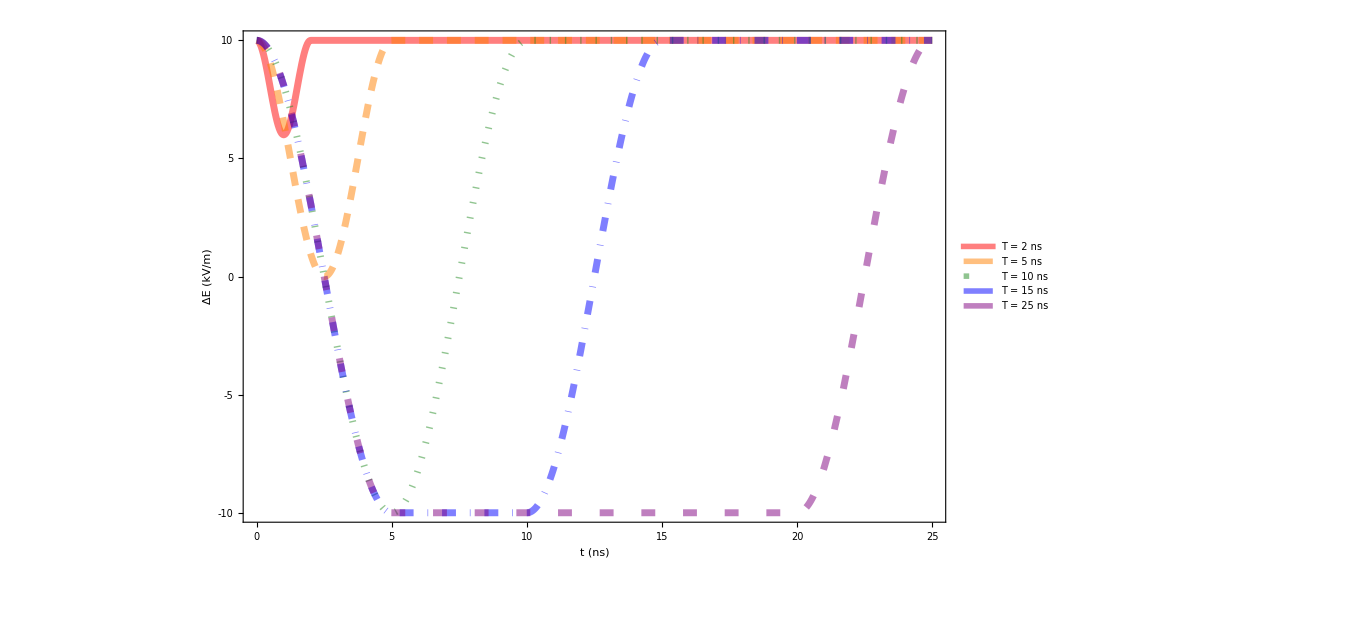

ZEpulses.eps

```mathematica
xTicks = LinTicks[0, 25, 5, 5, TickLengthScale->2,TickLabelStep->1];
xxTicks = LinTicks[0, 25, 5, 5, TickLengthScale->2,TickLabelStep->1, ShowTickLabels->False];
yTicks = LinTicks[-10, 10, 5, 5, TickLengthScale->2,TickLabelStep->1];
yyTicks = LinTicks[-10, 10, 5, 5, TickLengthScale->2,TickLabelStep->1, ShowTickLabels->False];
labelFontSize = 38;
legendFontSize = 32;
xLabel = "t (ns)";
yLabel = "ΔE (kV/m)";
curveThickness = 5;
curveOpacity = .5;

(* create legend *)
legend = Placed[{
Style["T = 2 ns",legendFontSize],
Style["T = 5 ns",legendFontSize],
Style["T = 10 ns",legendFontSize],
Style["T = 15 ns",legendFontSize],
Style["T = 25 ns",legendFontSize]
},{{.6, .3}, {0, 0}}];


Show[
Plot[{
EPulse[t*10^-9, 2*10^-9]/1000,
EPulse[t*10^-9, 5*10^-9]/1000,
EPulse[t*10^-9, 10*10^-9]/1000,
EPulse[t*10^-9, 15*10^-9]/1000,
EPulse[t*10^-9, 25*10^-9]/1000(*,

EPulse[t*10^-9, 15*10^-9]/1000 + Log[1 - HeavisideTheta[t - 20]],
EPulse[t*10^-9, 10*10^-9]/1000 + Log[1 - HeavisideTheta[t - 12]],
EPulse[t*10^-9, 5*10^-9]/1000 + Log[1 - HeavisideTheta[t - 7]],
EPulse[t*10^-9, 2*10^-9]/1000 + Log[1 - HeavisideTheta[t - 3]]*)
},
 {t, 0, 25},
PlotPoints->10,
PlotRange->All,LabelStyle->{FontFamily-> "Times"},
PlotStyle->{
{AbsoluteThickness[curveThickness],Opacity[curveOpacity], Red},
{AbsoluteThickness[curveThickness],Opacity[curveOpacity], Orange, AbsoluteDashing[{10, 10}]},
{AbsoluteThickness[curveThickness],Opacity[curveOpacity], ForestGreen, AbsoluteDashing[{1, 10}]},
{AbsoluteThickness[curveThickness],Opacity[curveOpacity], Blue, AbsoluteDashing[{10, 10, .1, 10}]},
{AbsoluteThickness[curveThickness],Opacity[curveOpacity], Purple, AbsoluteDashing[{10, 20}]},

(* second tracings *)
{AbsoluteThickness[curveThickness],Opacity[curveOpacity], Blue},
{AbsoluteThickness[curveThickness],Opacity[curveOpacity], Green},
{AbsoluteThickness[curveThickness],Opacity[curveOpacity], Orange},
{AbsoluteThickness[curveThickness],Opacity[curveOpacity], Red}
},
PlotLegends->legend,Axes->False
],
LabelStyle->{FontFamily-> "Times"},ImageSize->{10^3,10^3},
FrameStyle->Directive[Thick,labelFontSize,Black],Frame->True,
FrameLabel->{Style[xLabel,labelFontSize],Style[yLabel,labelFontSize]},
FrameTicks->{xTicks,yTicks,xxTicks,yyTicks}
]

Export["ZEpulses.eps", %]
```

## Generate R_z(ϕ) Spectrum

```mathematica
setVariables[];

Eamp[t_] := 0;
Bamp[t_] := 0;

ΔE = 10000;
(*Clear[UbaseLab];
UbaseLab = MatrixExp[-ⅈ*t*(HexactStatic /. t->0) // N];*)

(*defaultEnergies = energiesInOrder[HexactStatic /. t->0];
UbaseLab = MatrixExp[-ⅈ*t*DiagonalMatrix[defaultEnergies]];*)
UbaseLab = MatrixExp[-ⅈ*t*(HexactStatic /. t->0) // N];

ϕZ[T_?NumericQ] := (
Tmax = T;
T1 = Min[5*10^-9, Tmax/2];
T2 = Tmax - 2*T1;
ΔΔE = 20000*Min[1, T1/(5*10^-9)];
ΔE =10000 - ΔΔE*cosWindow[t, T1, Tmax] // N;


U= ConjugateTranspose[UbaseLab].(Λge /. t->t).findEvolutionOperator[HexactID, Tmax].ConjugateTranspose[Λge /. t->0];

ϕGenerated = Zangle[U[[{1, 2}, {1, 2}]] /. t->Tmax];

Pause[1];

(*ϕGenerated*)

Clear[deltaQ];
deltaQ[E0_?NumericQ] := (
ΔEold = ΔE;
Clear[ΔE];
(*output = energiesInOrder[HexactStatic /. {ΔE->E0}][[1]] - energiesInOrder[HexactStatic /. {ΔE->E0}][[2]];*)
output =  2π(B0*γe + Aexp/2) /. {ΔE->E0};
ΔE = ΔEold;
output
);

deltaQ0 = deltaQ[ΔE /. t->0];
ϕIdeal = NIntegrate[deltaQ[ΔE /. t->tt] - deltaQ0, {tt, 0, Tmax}];
Ftoϕ = fidelity2D[MatrixExp[-ⅈ*ϕIdeal*σZ/2], U[[{1, 2}, {1, 2}]]/.t->Tmax];

{ϕGenerated, ϕIdeal, Ftoϕ}
)


ϕs = {};
Do[AppendTo[ϕs, Join[{T}, ϕZ[T]]], {T, 0, 25*10^-9, .2*10^-9}];
ϕs

clearVariables[]
```

```mathematica
ϕs = {{0.,5.5477120587978756*^-17,0.,1.},{2.0000000000000003*^-10,0.00001772685195764519,0.000017677659442024492,1.0000000077056546},{4.0000000000000007*^-10,0.0000742496013081345,0.00007410834806008924,0.9999999942277251},{6.000000000000001*^-10,0.00017548047533921303,0.0001751413186509197,1.0000000608739745},{8.000000000000001*^-10,0.00032846040340683445,0.0003278312375820103,1.0000000788568872},{1.0000000000000003*^-9,0.0005417819002559245,0.0005407554725792116,1.000000204042944},{1.2000000000000002*^-9,0.0008260291746695551,0.0008244341715112934,1.0000002457754227},{1.4000000000000001*^-9,0.0011942278297685364,0.0011918931032074928,1.000000275471146},{1.6000000000000003*^-9,0.0016627468565956608,0.0016594275403157242,1.0000002695718149},{1.8000000000000004*^-9,0.0022522435999042037,0.0022476535013747118,1.0000002504545757},{2.0000000000000005*^-9,0.0029892440642729466,0.0029829763486529017,1.0000003716947863},{2.2000000000000003*^-9,0.003908117372053768,0.0038996760283157277,1.0000003816397156},{2.4000000000000004*^-9,0.00505420685802648,0.005042920243714172,1.0000003869105472},{2.6000000000000005*^-9,0.0064882670901827135,0.006473201418194571,1.0000004967357996},{2.8000000000000003*^-9,0.008293122281644976,0.00827300327450275,1.0000004906105358},{3.0000000000000004*^-9,0.01058405072022498,0.010557032675334583,1.0000005372253786},{3.2000000000000005*^-9,0.013524884668085858,0.01348827054712286,1.0000005234137186},{3.4000000000000007*^-9,0.01735394912385555,0.01730369534258762,1.0000005705983508},{3.600000000000001*^-9,0.022426576995080407,0.022356281462275834,1.000000606499253},{3.800000000000001*^-9,0.029285088630877407,0.029184326363261928,1.0000006251747902},{4.000000000000001*^-9,0.0387740061486439,0.038625061985680734,1.0000006330076077},{4.2*^-9,0.05221972924298651,0.05199154513198199,1.0000006638419228},{4.4000000000000005*^-9,0.0716668426305041,0.07130430080725125,1.0000006525554892},{4.600000000000001*^-9,0.10002110752718857,0.09943098882115867,1.0000007283408046},{4.800000000000001*^-9,0.14058005871694837,0.13962696957198895,1.0000006463916646},{5.000000000000001*^-9,0.1952284919375188,0.1937662382759247,1.000000408919752},{5.200000000000001*^-9,0.26217167054543966,0.2600919803736042,1.0000000996814107},{5.400000000000001*^-9,0.3363943040607555,0.3336330605927137,0.99999956236892},{5.6000000000000005*^-9,0.4128815995379535,0.40940146251535103,0.9999988337236904},{5.800000000000001*^-9,0.4886408897592919,0.4844248929649714,0.9999979469365365},{6.000000000000001*^-9,0.5624912695620728,0.5575384332525647,0.9999967440293482},{6.200000000000001*^-9,0.6342207497726849,0.6285392149639366,0.9999956047343025},{6.400000000000001*^-9,0.7040035645570782,0.6976053124977326,0.9999941498907319},{6.600000000000001*^-9,0.7721234716847437,0.7650209258899228,0.9999922854076939},{6.800000000000001*^-9,0.838863995612658,0.8310691221970478,0.9999905702344029},{7.0000000000000015*^-9,0.904474668471706,0.8959975416899536,0.9999877419398114},{7.200000000000002*^-9,0.9691621708719532,0.9600123377978265,0.999985941232462},{7.400000000000001*^-9,1.033096498694723,1.0232817856632257,0.9999846525396692},{7.600000000000002*^-9,1.0964161864758115,1.0859423800359,0.9999821504131308},{7.800000000000002*^-9,1.1592320688564202,1.1481048531312312,0.9999795382187987},{8.000000000000002*^-9,1.221635140983852,1.2098593353287665,0.9999776236322113},{8.2*^-9,1.283701993066335,1.271279541265566,0.9999727744712736},{8.4*^-9,1.3454918760188053,1.3324260888972286,0.9999688759715946},{8.600000000000001*^-9,1.407053680387389,1.39334910449404,0.9999669492850078},{8.800000000000001*^-9,1.4684304153350463,1.4540902649360636,0.9999663508483289},{9.000000000000001*^-9,1.5296613612577379,1.514684402159594,0.9999622959696453},{9.200000000000001*^-9,1.5907723425844986,1.5751607682680622,0.9999583476728793},{9.400000000000001*^-9,1.6517870435966973,1.6355440393966423,0.9999567506612342},{9.600000000000002*^-9,1.712734003714385,1.6958551170945495,0.9999502027304478},{9.800000000000002*^-9,1.7736223707111427,1.7561117681362304,0.9999466588659076},{1.0000000000000002*^-8,1.8344710820559125,1.816329149851585,0.9999436235519394},{1.0200000000000002*^-8,1.9078809454768157,1.8889823232863816,0.9999411237558367},{1.0400000000000002*^-8,1.981297254902029,1.9616354364189428,0.9999347783416447},{1.0600000000000002*^-8,2.05471276376332,2.0342886639803752,0.9999290369266984},{1.0800000000000002*^-8,2.128122451128953,2.1069418463079774,0.9999257390411749},{1.1000000000000003*^-8,2.201539275800471,2.179594923017559,0.9999190059083143},{1.1200000000000001*^-8,2.2749544427677044,2.2522481456762047,0.999912890846333},{1.1400000000000001*^-8,2.3483640403397885,2.324901428322078,0.9999085600360482},{1.1600000000000001*^-8,2.421781304211801,2.3975543245747826,0.9999014693650956},{1.1800000000000001*^-8,2.4951960413355168,2.4702078765649085,0.9998950921571561},{1.2000000000000002*^-8,2.568605661437108,2.5428605943819367,0.9998895952694418},{1.2200000000000002*^-8,2.642023316766618,2.615513992344393,0.9998822604019815},{1.2400000000000002*^-8,2.715437586246758,2.6881671087099295,0.9998754487125483},{1.2600000000000002*^-8,2.7888473484863745,2.76082026936071,0.9998688859920666},{1.2800000000000002*^-8,2.8622653447206003,2.833473525703134,0.9998613672567165},{1.3000000000000002*^-8,2.935679140854093,2.90612662947157,0.9998540334943651},{1.3200000000000002*^-8,3.009089124333974,2.978779795130581,0.9998464488888992},{1.3400000000000003*^-8,3.0825073315003477,3.0514316584425547,0.9998388073561195},{1.3600000000000003*^-8,-3.1272646684986096,3.124086100221759,0.9998308573439996},{1.3800000000000003*^-8,-3.05385436426121,3.1967393845185352,0.9998223022355284},{1.4000000000000003*^-8,-2.9804360311811733,3.2693923197074577,0.9998146188905874},{1.4200000000000003*^-8,-2.9070231803783693,3.342045764579095,0.9998059013296408},{1.4400000000000003*^-8,-2.8336124714461692,3.4146989122498193,0.9997964267559891},{1.4600000000000002*^-8,-2.760194099382315,3.4873519146795102,0.9997886843088973},{1.4800000000000002*^-8,-2.6867816539270204,3.5600052049918465,0.9997791395146762},{1.5000000000000002*^-8,-2.6133705139469825,3.6326587197348834,0.9997688635612003},{1.5200000000000004*^-8,-2.5399522459072807,3.705311188062658,0.9997610496766308},{1.5400000000000002*^-8,-2.466540149260233,3.7779645989673516,0.999750397104641},{1.5600000000000004*^-8,-2.3931285264296993,3.850617814874816,0.9997396043523135},{1.5800000000000003*^-8,-2.3197104470981547,3.9232712592739674,0.9997316483258835},{1.6000000000000004*^-8,-2.2462986098237168,3.995924129658688,0.9997201766435168},{1.6200000000000003*^-8,-2.172886485991106,4.068576976327817,0.9997085880294228},{1.64*^-8,-2.0994686763777133,4.141228737087862,0.9997005115689026},{1.6600000000000003*^-8,-2.0260570094089783,4.213883851679777,0.9996880552404456},{1.68*^-8,-1.9526444275642445,4.286537425475468,0.9996760030927101},{1.7000000000000003*^-8,-1.8792269982966743,4.35918970448703,0.9996677206977109},{1.7200000000000002*^-8,-1.8058153981769063,4.431842502963518,0.999654158376063},{1.7400000000000004*^-8,-1.7324023678735423,4.504496154283458,0.9996417107276356},{1.7600000000000002*^-8,-1.6589853651293565,4.577149700286601,0.999633146601915},{1.7800000000000004*^-8,-1.5855737233762204,4.649802879137729,0.9996185070496382},{1.8000000000000002*^-8,-1.5121602950513215,4.72245475660293,0.9996057109214453},{1.8200000000000004*^-8,-1.4387437572192583,4.79510749606442,0.9995967846067498},{1.8400000000000003*^-8,-1.3653319811285727,4.867762036777745,0.9995811027870003},{1.8600000000000004*^-8,-1.2919182578175097,4.940415420289787,0.9995681510308067},{1.8800000000000003*^-8,-1.2185022297934696,5.013068682443201,0.9995587186279892},{1.9000000000000005*^-8,-1.1450902105530656,5.085721894189314,0.9995419664180729},{1.9200000000000003*^-8,-1.0716762502642967,5.158374768085093,0.999528875626353},{1.9400000000000002*^-8,-0.9982607185871046,5.231027690146343,0.9995188115431957},{1.9600000000000003*^-8,-0.924848370573709,5.303681076621936,0.9995011444652138},{1.9800000000000002*^-8,-0.8514342704561074,5.376334333441098,0.9994878087958103},{2.0000000000000004*^-8,-0.7780192125320975,5.44898744955473,0.9994771263420922},{2.0200000000000002*^-8,-0.704606477738486,5.521640617446304,0.9994585254308173},{2.0400000000000004*^-8,-0.6311923678798654,5.594293788983587,0.9994451867929117},{2.0600000000000002*^-8,-0.5577777541441481,5.666946955889916,0.9994336325988886},{2.0800000000000004*^-8,-0.48436455746302487,5.739600068110215,0.9994142473025189},{2.1000000000000003*^-8,-0.41095051292275375,5.812253353154013,0.999400761388372},{2.1200000000000005*^-8,-0.33753627322773766,5.884906461665708,0.9993883611379438},{2.1400000000000003*^-8,-0.26412258609579997,5.957559486899852,0.9993682483051931},{2.1600000000000005*^-8,-0.19070870979191504,6.030212809664255,0.9993546349901277},{2.1800000000000003*^-8,-0.11729476820703674,6.102866106481112,0.9993413140162866},{2.2000000000000005*^-8,-0.04388059228735957,6.175519052843602,0.9993206096423318},{2.2200000000000004*^-8,0.029532999510449305,6.248172091971582,0.9993068251802032},{2.2400000000000002*^-8,0.1029467294146262,6.320825441565498,0.9992924844697832},{2.2600000000000004*^-8,0.17636141273388958,6.393478806068795,0.9992712853078435},{2.2800000000000002*^-8,0.24977466659855938,6.4661318900374605,0.9992572580815668},{2.3000000000000004*^-8,0.32318828503621777,6.538784727772066,0.9992418719529068},{2.3200000000000003*^-8,0.39660343528210656,6.611437952275864,0.9992202545610122},{2.3400000000000004*^-8,0.4700162818384689,6.684091353586995,0.9992057355080771},{2.3600000000000003*^-8,0.5434298895508246,6.756744670232372,0.9991895130547652},{2.3800000000000005*^-8,0.6168454429493517,6.8293976403153325,0.9991675898432157},{2.4000000000000003*^-8,0.690257816523716,6.902050554028917,0.9991526401275599},{2.4200000000000005*^-8,0.7636715194386718,6.974703816433987,0.99913532167421},{2.4400000000000003*^-8,0.8370874395200518,7.0473571963414745,0.9991131153853787},{2.4600000000000005*^-8,0.9104993371095899,7.120010462209358,0.9990978795769372},{2.4800000000000004*^-8,0.9839132265430103,7.192663400347504,0.9990794101471968},{2.5000000000000005*^-8,1.057329417288226,7.265316447969079,0.999057016056725}}
```

{{0.,5.54771×10^-17,0.,1.},{2.×10^-10,0.0000177269,0.0000176777,1.},{4.×10^-10,0.0000742496,0.0000741083,1.},{6.×10^-10,0.00017548,0.000175141,1.},{8.×10^-10,0.00032846,0.000327831,1.},{1.×10^-9,0.000541782,0.000540755,1.},{1.2×10^-9,0.000826029,0.000824434,1.},{1.4×10^-9,0.00119423,0.00119189,1.},{1.6×10^-9,0.00166275,0.00165943,1.},{1.8×10^-9,0.00225224,0.00224765,1.},{2.×10^-9,0.00298924,0.00298298,1.},{2.2×10^-9,0.00390812,0.00389968,1.},{2.4×10^-9,0.00505421,0.00504292,1.},{2.6×10^-9,0.00648827,0.0064732,1.},{2.8×10^-9,0.00829312,0.008273,1.},{3.×10^-9,0.0105841,0.010557,1.},{3.2×10^-9,0.0135249,0.0134883,1.},{3.4×10^-9,0.0173539,0.0173037,1.},{3.6×10^-9,0.0224266,0.0223563,1.},{3.8×10^-9,0.0292851,0.0291843,1.},{4.×10^-9,0.038774,0.0386251,1.},{4.2×10^-9,0.0522197,0.0519915,1.},{4.4×10^-9,0.0716668,0.0713043,1.},{4.6×10^-9,0.100021,0.099431,1.},{4.8×10^-9,0.14058,0.139627,1.},{5.×10^-9,0.195228,0.193766,1.},{5.2×10^-9,0.262172,0.260092,1.},{5.4×10^-9,0.336394,0.333633,1.},{5.6×10^-9,0.412882,0.409401,0.999999},{5.8×10^-9,0.488641,0.484425,0.999998},{6.×10^-9,0.562491,0.557538,0.999997},{6.2×10^-9,0.634221,0.628539,0.999996},{6.4×10^-9,0.704004,0.697605,0.999994},{6.6×10^-9,0.772123,0.765021,0.999992},{6.8×10^-9,0.838864,0.831069,0.999991},{7.×10^-9,0.904475,0.895998,0.999988},{7.2×10^-9,0.969162,0.960012,0.999986},{7.4×10^-9,1.0331,1.02328,0.999985},{7.6×10^-9,1.09642,1.08594,0.999982},{7.8×10^-9,1.15923,1.1481,0.99998},{8.×10^-9,1.22164,1.20986,0.999978},{8.2×10^-9,1.2837,1.27128,0.999973},{8.4×10^-9,1.34549,1.33243,0.999969},{8.6×10^-9,1.40705,1.39335,0.999967},{8.8×10^-9,1.46843,1.45409,0.999966},{9.×10^-9,1.52966,1.51468,0.999962},{9.2×10^-9,1.59077,1.57516,0.999958},{9.4×10^-9,1.65179,1.63554,0.999957},{9.6×10^-9,1.71273,1.69586,0.99995},{9.8×10^-9,1.77362,1.75611,0.999947},{1.×10^-8,1.83447,1.81633,0.999944},{1.02×10^-8,1.90788,1.88898,0.999941},{1.04×10^-8,1.9813,1.96164,0.999935},{1.06×10^-8,2.05471,2.03429,0.999929},{1.08×10^-8,2.12812,2.10694,0.999926},{1.1×10^-8,2.20154,2.17959,0.999919},{1.12×10^-8,2.27495,2.25225,0.999913},{1.14×10^-8,2.34836,2.3249,0.999909},{1.16×10^-8,2.42178,2.39755,0.999901},{1.18×10^-8,2.4952,2.47021,0.999895},{1.2×10^-8,2.56861,2.54286,0.99989},{1.22×10^-8,2.64202,2.61551,0.999882},{1.24×10^-8,2.71544,2.68817,0.999875},{1.26×10^-8,2.78885,2.76082,0.999869},{1.28×10^-8,2.86227,2.83347,0.999861},{1.3×10^-8,2.93568,2.90613,0.999854},{1.32×10^-8,3.00909,2.97878,0.999846},{1.34×10^-8,3.08251,3.05143,0.999839},{1.36×10^-8,-3.12726,3.12409,0.999831},{1.38×10^-8,-3.05385,3.19674,0.999822},{1.4×10^-8,-2.98044,3.26939,0.999815},{1.42×10^-8,-2.90702,3.34205,0.999806},{1.44×10^-8,-2.83361,3.4147,0.999796},{1.46×10^-8,-2.76019,3.48735,0.999789},{1.48×10^-8,-2.68678,3.56001,0.999779},{1.5×10^-8,-2.61337,3.63266,0.999769},{1.52×10^-8,-2.53995,3.70531,0.999761},{1.54×10^-8,-2.46654,3.77796,0.99975},{1.56×10^-8,-2.39313,3.85062,0.99974},{1.58×10^-8,-2.31971,3.92327,0.999732},{1.6×10^-8,-2.2463,3.99592,0.99972},{1.62×10^-8,-2.17289,4.06858,0.999709},{1.64×10^-8,-2.09947,4.14123,0.999701},{1.66×10^-8,-2.02606,4.21388,0.999688},{1.68×10^-8,-1.95264,4.28654,0.999676},{1.7×10^-8,-1.87923,4.35919,0.999668},{1.72×10^-8,-1.80582,4.43184,0.999654},{1.74×10^-8,-1.7324,4.5045,0.999642},{1.76×10^-8,-1.65899,4.57715,0.999633},{1.78×10^-8,-1.58557,4.6498,0.999619},{1.8×10^-8,-1.51216,4.72245,0.999606},{1.82×10^-8,-1.43874,4.79511,0.999597},{1.84×10^-8,-1.36533,4.86776,0.999581},{1.86×10^-8,-1.29192,4.94042,0.999568},{1.88×10^-8,-1.2185,5.01307,0.999559},{1.9×10^-8,-1.14509,5.08572,0.999542},{1.92×10^-8,-1.07168,5.15837,0.999529},{1.94×10^-8,-0.998261,5.23103,0.999519},{1.96×10^-8,-0.924848,5.30368,0.999501},{1.98×10^-8,-0.851434,5.37633,0.999488},{2.×10^-8,-0.778019,5.44899,0.999477},{2.02×10^-8,-0.704606,5.52164,0.999459},{2.04×10^-8,-0.631192,5.59429,0.999445},{2.06×10^-8,-0.557778,5.66695,0.999434},{2.08×10^-8,-0.484365,5.7396,0.999414},{2.1×10^-8,-0.410951,5.81225,0.999401},{2.12×10^-8,-0.337536,5.88491,0.999388},{2.14×10^-8,-0.264123,5.95756,0.999368},{2.16×10^-8,-0.190709,6.03021,0.999355},{2.18×10^-8,-0.117295,6.10287,0.999341},{2.2×10^-8,-0.0438806,6.17552,0.999321},{2.22×10^-8,0.029533,6.24817,0.999307},{2.24×10^-8,0.102947,6.32083,0.999292},{2.26×10^-8,0.176361,6.39348,0.999271},{2.28×10^-8,0.249775,6.46613,0.999257},{2.3×10^-8,0.323188,6.53878,0.999242},{2.32×10^-8,0.396603,6.61144,0.99922},{2.34×10^-8,0.470016,6.68409,0.999206},{2.36×10^-8,0.54343,6.75674,0.99919},{2.38×10^-8,0.616845,6.8294,0.999168},{2.4×10^-8,0.690258,6.90205,0.999153},{2.42×10^-8,0.763672,6.9747,0.999135},{2.44×10^-8,0.837087,7.04736,0.999113},{2.46×10^-8,0.910499,7.12001,0.999098},{2.48×10^-8,0.983913,7.19266,0.999079},{2.5×10^-8,1.05733,7.26532,0.999057}}

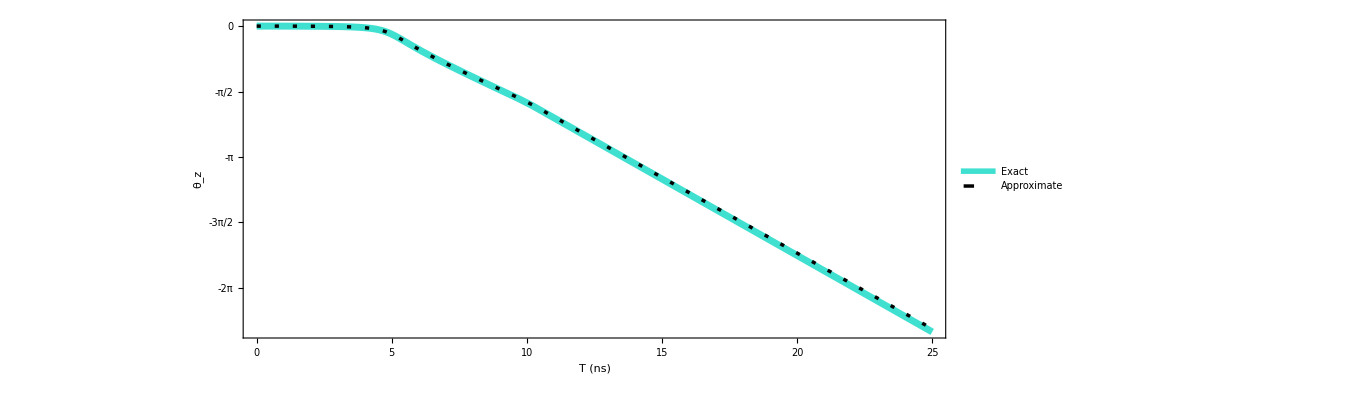

zPhase.eps

```mathematica
unravel[input_] := (
output = input;
Do[(
If[output[[i + 1]] - output[[i]] > π, output[[i + 1;;]] = output[[i + 1;;]] - 2π];
If[output[[i + 1]] - output[[i]] < -π, output[[i + 1;;]] = output[[i + 1;;]] + 2π];
),{i, Length[input] - 1}
];
output
)
ϕs[[All, 2]] = unravel[ϕs[[All, 2]]];

ϕ = Interpolation[ϕs[[All, {1, 2}]]];
ϕApprox = Interpolation[ϕs[[All, {1, 3}]]];



(* GENERATE zPhase PLOT *)
xTicks = LinTicks[0, 25, 5, 5, TickLengthScale->2,TickLabelStep->1];
xxTicks = LinTicks[0, 25, 5, 5, TickLengthScale->2,TickLabelStep->1, ShowTickLabels->False];
yTicks = {{0.,"0",{0.01,0},{}},{1.5707963267948966,"π/2",{0.01,0},{}},{3.141592653589793,"π",{0.01,0},{}},{4.71238898038469,"3π/2",{0.01,0},{}},{6.283185307179586,"2π",{0.01,0},{}},{0.39269908169872414,"",{0.005,0},{}},{0.7853981633974483,"",{0.005,0},{}},{1.1780972450961724,"",{0.005,0},{}},{1.9634954084936207,"",{0.005,0},{}},{2.356194490192345,"",{0.005,0},{}},{2.748893571891069,"",{0.005,0},{}},{3.5342917352885173,"",{0.005,0},{}},{3.9269908169872414,"",{0.005,0},{}},{4.319689898685965,"",{0.005,0},{}},{5.105088062083414,"",{0.005,0},{}},{5.497787143782138,"",{0.005,0},{}},{5.890486225480862,"",{0.005,0},{}}};
yyTicks = {{0.,"",{0.01,0},{}},{1.5707963267948966,"",{0.01,0},{}},{3.141592653589793,"",{0.01,0},{}},{4.71238898038469,"",{0.01,0},{}},{6.283185307179586,"",{0.01,0},{}},{0.39269908169872414,"",{0.005,0},{}},{0.7853981633974483,"",{0.005,0},{}},{1.1780972450961724,"",{0.005,0},{}},{1.9634954084936207,"",{0.005,0},{}},{2.356194490192345,"",{0.005,0},{}},{2.748893571891069,"",{0.005,0},{}},{3.5342917352885173,"",{0.005,0},{}},{3.9269908169872414,"",{0.005,0},{}},{4.319689898685965,"",{0.005,0},{}},{5.105088062083414,"",{0.005,0},{}},{5.497787143782138,"",{0.005,0},{}},{5.890486225480862,"",{0.005,0},{}}};

yTicks = {{0.,"0",{0.01,0},{}},{1.5707963267948966,"-π/2",{0.01,0},{}},{3.141592653589793,"-π",{0.01,0},{}},{4.71238898038469,"-3π/2",{0.01,0},{}},{6.283185307179586,"-2π",{0.01,0},{}},{0.39269908169872414,"",{0.005,0},{}},{0.7853981633974483,"",{0.005,0},{}},{1.1780972450961724,"",{0.005,0},{}},{1.9634954084936207,"",{0.005,0},{}},{2.356194490192345,"",{0.005,0},{}},{2.748893571891069,"",{0.005,0},{}},{3.5342917352885173,"",{0.005,0},{}},{3.9269908169872414,"",{0.005,0},{}},{4.319689898685965,"",{0.005,0},{}},{5.105088062083414,"",{0.005,0},{}},{5.497787143782138,"",{0.005,0},{}},{5.890486225480862,"",{0.005,0},{}}};
yyTicks = yTicks;
Do[(
yTicks[[i]][[1]] = -yTicks[[i]][[1]];
yTicks[[i]][[3]][[1]] = yTicks[[i]][[3]][[1]]*2;
yyTicks[[i]][[1]] = -yyTicks[[i]][[1]];
yyTicks[[i]][[2]] = "";
yyTicks[[i]][[3]][[1]] = yyTicks[[i]][[3]][[1]]*2;
)
,{i, Length[yTicks]}];

labelFontSize = 38;
legendFontSize = 38;
xLabel = "T (ns)";
yLabel = "θ_z";
curveThickness = 5;
curveOpacity = .5;

(* create legend *)
legend = Placed[{
Style["Exact",legendFontSize],
Style["Approximate",legendFontSize]
},{{.1, .2}, {0, 0}}];


Show[
Plot[{
-ϕ[T*10^-9],
-ϕApprox[T*10^-9]
},
 {T, 0, 25},
PlotRange->{{0, 25},All},LabelStyle->{FontFamily-> "Times"},
PlotStyle->{
{AbsoluteThickness[curveThickness],Turquoise},
{AbsoluteThickness[curveThickness/2],AbsoluteDashing[{3,10}],Black}
},
PlotLegends->legend,Axes->False
],
LabelStyle->{FontFamily-> "Times"},ImageSize->{1000, 1000},AspectRatio->.4,
FrameStyle->Directive[Thick,labelFontSize,Black],Frame->True,
FrameLabel->{Style[xLabel,labelFontSize],Style[yLabel,labelFontSize]},
FrameTicks->{xTicks,yTicks,xxTicks,yyTicks}
]

Export["zPhase.eps", %]
```

## Find fidelity of a Z-gate with noise

```mathematica
setVariables[];

Eamp[t_] := 0;
Bamp[t_] := 0;

ΔE = 10000;
UbaseLab = MatrixExp[-ⅈ*t*(HexactStatic /. t->0) // N];

ZfidelityWithNoise[T_?NumericQ, ϕTarget_, δE_] := (
statusString = "Error of " <> ToString[δE] <> "V/m          ";
Tmax = T;
T1 = Min[5*10^-9, Tmax/2];
T2 = Tmax - 2*T1;
ΔΔE = 20000*Min[1, T1/(5*10^-9)];
ΔE =10000 - ΔΔE*cosWindow[t, T1, Tmax] + δE // N;

U= ConjugateTranspose[UbaseLab].(Λge /. t->t).findEvolutionOperator[HexactID, Tmax].ConjugateTranspose[Λge /. t->0];

F = fidelity2D[U[[{1, 2}, {1, 2}]] /. t-> Tmax, MatrixExp[-ⅈ*ϕTarget*σZ/2]];

Pause[1];

F
)

(*RzFidelitiesWithNoise = {Table[{δ, ZfidelityWithNoise[6.632*10^-9, π/4, δ]}, {δ, -1000, 1000, 20}],
Table[{δ, ZfidelityWithNoise[13.560*10^-9, π, δ]}, {δ, -1000, 1000, 20}],
Table[{δ, ZfidelityWithNoise[22.116*10^-9, 2π, δ]}, {δ, -1000, 1000, 20}]};

RzFidelitiesWithNoise*)

RzFidelitiesWithNoiseExtra = {Table[{δ, ZfidelityWithNoise[6.632*10^-9, π/4, δ]}, {δ, -20010, 1000, 20}],
Table[{δ, ZfidelityWithNoise[13.560*10^-9, π, δ]}, {δ, -1000, 1000, 20}],
Table[{δ, ZfidelityWithNoise[22.116*10^-9, 2π, δ]}, {δ, -1000, 1000, 20}]};

RzFidelitiesWithNoise

clearVariables[]
```

0.935496

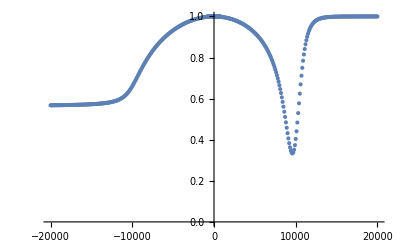

```mathematica
RzFidelitiesWithNoiseNeg = {{{-20000,0.6380811346232037},{-19900,0.6381162083824705},{-19800,0.6381521818434344},{-19700,0.6381890341395422},{-19600,0.6382268118384251},{-19500,0.6382655691518361},{-19400,0.6383052894474803},{-19300,0.6383460746997982},{-19200,0.6383879099322632},{-19100,0.6384308411211179},{-19000,0.6384749537783387},{-18900,0.6385202142419875},{-18800,0.6385667406309155},{-18700,0.6386145476691244},{-18600,0.6386636589036081},{-18500,0.6387141991728875},{-18400,0.6387661376745866},{-18300,0.638819587537961},{-18200,0.6388746184976049},{-18100,0.6389312166335894},{-18000,0.6389895578329647},{-17900,0.6390496260445849},{-17800,0.6391115190053307},{-17700,0.6391753704170485},{-17600,0.6392411469711765},{-17500,0.6393090573870825},{-17400,0.6393791444321186},{-17300,0.6394514512484589},{-17200,0.6395262108632145},{-17100,0.6396033842828805},{-17000,0.6396826563239577},{-16900,0.6397650745612753},{-16800,0.6398502991809362},{-16700,0.6399386216762118},{-16600,0.640030048327769},{-16500,0.6401247268758301},{-16400,0.6402229852222785},{-16300,0.6403247602172162},{-16200,0.6404304304232031},{-16100,0.6405401745804237},{-16000,0.6406540341205129},{-15900,0.6407725351617704},{-15800,0.640895677097639},{-15700,0.6410237654980946},{-15600,0.6411572962250054},{-15500,0.6412962153661905},{-15400,0.6414411527356467},{-15300,0.6415924244714415},{-15200,0.6417501157648644},{-15100,0.6419151078144558},{-15000,0.6420875020152722},{-14900,0.6422677351138697},{-14800,0.6424567699495722},{-14700,0.6426545579851775},{-14600,0.6428614838319897},{-14500,0.6430794376343327},{-14400,0.6433080168867724},{-14300,0.64354871940911},{-14200,0.6438021392412714},{-14100,0.6440687118018851},{-14000,0.6443504222564514},{-13900,0.6446476294025201},{-13800,0.6449614283650476},{-13700,0.6452941913228837},{-13600,0.645646175767934},{-13500,0.6460193472032876},{-13400,0.6464164714154351},{-13300,0.6468378664685682},{-13200,0.6472865905521933},{-13100,0.6477659341942921},{-13000,0.648276086269771},{-12900,0.6488220203017732},{-12800,0.6494078011239348},{-12700,0.6500343864660625},{-12600,0.6507075260729847},{-12500,0.6514333303140589},{-12400,0.6522133933856008},{-12300,0.6530547949816734},{-12200,0.6539669227228216},{-12100,0.6549527431836046},{-12000,0.6560196491995727},{-11900,0.6571818149513564},{-11800,0.6584465164013511},{-11700,0.6598196145312722},{-11600,0.6613179527537019},{-11500,0.6629596763384152},{-11400,0.6647522064264415},{-11300,0.6667069400078321},{-11200,0.6688478654661427},{-11100,0.6711984745159065},{-11000,0.673771511565149},{-10900,0.676577181301389},{-10800,0.6796331925836944},{-10700,0.6829621752421171},{-10600,0.6865828086402744},{-10500,0.6905052454576374},{-10400,0.6947321467660622},{-10300,0.6992605340629137},{-10200,0.7040819494789209},{-10100,0.7091814181370026},{-10000,0.7145369535383896},{-9900,0.7201209301668966},{-9800,0.7259037698850852},{-9700,0.7318567883820017},{-9600,0.7379455460286063},{-9500,0.7441152209543659},{-9400,0.7503067904002017},{-9300,0.7565121380122544},{-9200,0.7627285816419223},{-9100,0.7688769507233576},{-9000,0.7749590014912151},{-8900,0.7809739622548478},{-8800,0.786868084210055},{-8700,0.7926769031996428},{-8600,0.7983508885721738},{-8500,0.8039168172995688},{-8400,0.8093570457734007},{-8300,0.814665775330357},{-8200,0.8198596129980797},{-8100,0.8249273239792856},{-8000,0.829868308584422},{-7900,0.8346932193575377},{-7800,0.8394033939323269},{-7700,0.8440010386762344},{-7600,0.8484868740304387},{-7500,0.8528652641391},{-7400,0.8571393597398682},{-7300,0.8613136482930008},{-7200,0.8653902042135609},{-7100,0.8693727133695592},{-7000,0.8732643597683192},{-6900,0.877066349647339},{-6800,0.880783985585883},{-6700,0.8844172531193794},{-6600,0.8879699255452215},{-6500,0.8914476663247164},{-6400,0.8948464196596497},{-6300,0.8981736292226913},{-6200,0.9014265228170038},{-6100,0.9046115138651469},{-6000,0.9077288745080994},{-5900,0.9107780068844917},{-5800,0.9137660995482286},{-5700,0.9166871062339492},{-5600,0.9195502909927229},{-5500,0.9223503092642407},{-5400,0.9250933460432048},{-5300,0.9277783308089085},{-5200,0.9304054269455727},{-5100,0.9329798980869614},{-5000,0.9354961714221617},{-4900,0.9379621627142304},{-4800,0.9403748813122881},{-4700,0.9427324553690537},{-4600,0.9450452555604701},{-4500,0.9473012515161289},{-4400,0.9495098254478476},{-4300,0.951672959315884},{-4200,0.9537833738930985},{-4100,0.9558439298734829},{-4000,0.9578633121658886},{-3900,0.9598337299245975},{-3800,0.9617523984562931},{-3700,0.9636284259234691},{-3600,0.9654610461108183},{-3500,0.9672470237428001},{-3400,0.9689832871458224},{-3300,0.970674590510745},{-3200,0.9723245244197961},{-3100,0.9739302614443025},{-3000,0.9754905450060846},{-2900,0.9770033288531558},{-2800,0.978469865426604},{-2700,0.9798930731228694},{-2600,0.9812714997445778},{-2500,0.9826060362782982},{-2400,0.9838963043905546},{-2300,0.9851402938825979},{-2200,0.9863386645315506},{-2100,0.9874908993463674},{-2000,0.9885963115668228},{-1900,0.9896550642427334},{-1800,0.990666843709427},{-1700,0.9916310371125701},{-1600,0.9925471071617717},{-1500,0.9934148830128052},{-1400,0.9942332263396501},{-1300,0.9950013578956887},{-1200,0.9957188533478805},{-1100,0.9963848276970877},{-1000,0.9969982052857225}},{{-20000,0.572724865489359},{-19900,0.5727675441207876},{-19800,0.5728112476375815},{-19700,0.572856015302337},{-19600,0.5729018622619999},{-19500,0.5729488529945213},{-19400,0.5729970274861982},{-19300,0.573046406791615},{-19200,0.5730970646489559},{-19100,0.5731490170789066},{-19000,0.5731997896519994},{-18900,0.5732565183590019},{-18800,0.5733103575623184},{-18700,0.5733678499779669},{-18600,0.5734269091998823},{-18500,0.5734876670538368},{-18400,0.5735499800331383},{-18300,0.5736143444835442},{-18200,0.5736801373758726},{-18100,0.5737479117383841},{-18000,0.5738176907317738},{-17900,0.573889547178893},{-17800,0.5739635534354428},{-17700,0.5740397980900617},{-17600,0.5741183860736128},{-17500,0.5741994242445669},{-17400,0.5742830181542293},{-17300,0.5743692793788179},{-17200,0.5744583323506074},{-17100,0.5745503116948076},{-17000,0.5746453278976924},{-16900,0.574743538345385},{-16800,0.57484508760045},{-16700,0.5749501482467632},{-16600,0.5750575457838452},{-16500,0.5751715759816923},{-16400,0.5752878799448398},{-16300,0.5754074228401124},{-16200,0.5755326815848476},{-16100,0.575662075626628},{-16000,0.575797295044852},{-15900,0.5759375003049653},{-15800,0.5760830744292506},{-15700,0.5762346223004938},{-15600,0.5763924118907504},{-15500,0.5765567766124224},{-15400,0.5767280781236961},{-15300,0.5769067255809052},{-15200,0.5770931409713255},{-15100,0.5772878779605521},{-15000,0.5774913906435742},{-14900,0.5777043598802851},{-14800,0.5779264006487175},{-14700,0.5781598932794041},{-14600,0.5784046830164408},{-14500,0.5786614542582735},{-14400,0.5789326993000029},{-14300,0.579214472313544},{-14200,0.5795131000938217},{-14100,0.5798279981021156},{-14000,0.5801598305193749},{-13900,0.5805102404711555},{-13800,0.5808805844659721},{-13700,0.5812724554226707},{-13600,0.5816876773330139},{-13500,0.5821282527882038},{-13400,0.5825962814267888},{-13300,0.5830933629988824},{-13200,0.5836231670483873},{-13100,0.5841875526005833},{-13000,0.5847905205011277},{-12900,0.5854364238381788},{-12800,0.58613175951252},{-12700,0.586869046094054},{-12600,0.5876655541160026},{-12500,0.5885227775243035},{-12400,0.5894471679939339},{-12300,0.590445575171613},{-12200,0.5915252815006036},{-12100,0.5926947345498795},{-12000,0.593963127839422},{-11900,0.5953428964338732},{-11800,0.5968450856495948},{-11700,0.5984827439430056},{-11600,0.6002755710344779},{-11500,0.6022268020138606},{-11400,0.6043658427008893},{-11300,0.6067091344943464},{-11200,0.609279948547871},{-11100,0.6120945969454176},{-11000,0.6151789951021854},{-10900,0.6185612574706464},{-10800,0.6222508871801309},{-10700,0.6262865809250876},{-10600,0.6306726405841152},{-10500,0.6354270842157663},{-10400,0.6405713838876221},{-10300,0.6460770732450042},{-10200,0.6519707581854994},{-10100,0.6582181826869986},{-10000,0.6647819300694541},{-9900,0.6716695074003881},{-9800,0.6788149813664044},{-9700,0.6861547394040765},{-9600,0.6936612736847143},{-9500,0.7013044444831114},{-9400,0.7090099634950695},{-9300,0.7167327705557132},{-9200,0.7244448432493489},{-9100,0.7321129075232722},{-9000,0.7396970467279305},{-8900,0.7471809201406321},{-8800,0.7545379187508947},{-8700,0.7617690784994737},{-8600,0.768852179179274},{-8500,0.7757778331539273},{-8400,0.7825477022174061},{-8300,0.7891681376348296},{-8200,0.7956149443112098},{-8100,0.8019000845236383},{-8000,0.8080308363904292},{-7900,0.8140017874901411},{-7800,0.8198201065263745},{-7700,0.8254904488251027},{-7600,0.8310122188670005},{-7500,0.8363970526975957},{-7400,0.8416345525246585},{-7300,0.8467407220435839},{-7200,0.8517152186261084},{-7100,0.8565667779383165},{-7000,0.8612895098789753},{-6900,0.8658940704663987},{-6800,0.8703826389416789},{-6700,0.874758439358812},{-6600,0.879029434922459},{-6500,0.8831830743718908},{-6400,0.8872379103143944},{-6300,0.8911918695683877},{-6200,0.8950488817683824},{-6100,0.8988067977124687},{-6000,0.9024740574941961},{-5900,0.9060495428915429},{-5800,0.9095366299275405},{-5700,0.912935735475352},{-5600,0.9162509721572569},{-5500,0.9194826926693779},{-5400,0.9226332918530051},{-5300,0.9257058457566704},{-5200,0.9286989557708387},{-5100,0.9316162945378252},{-5000,0.9344588575627104},{-4900,0.9372288314221322},{-4800,0.9399265246806239},{-4700,0.9425510363969429},{-4600,0.9451085476575122},{-4500,0.9475968782431048},{-4400,0.9500177865425412},{-4300,0.9523741130694013},{-4200,0.9546625573451785},{-4100,0.9568877628410478},{-4000,0.9590503089159981},{-3900,0.9611493637568702},{-3800,0.9631876297364388},{-3700,0.96516466361792},{-3600,0.9670810742740171},{-3500,0.968937701282387},{-3400,0.9707366211150823},{-3300,0.9724760679778894},{-3200,0.9741588222556833},{-3100,0.9757847741056086},{-3000,0.9773537920837074},{-2900,0.9788668991224203},{-2800,0.9803255820284358},{-2700,0.9817282028828629},{-2600,0.9830767374017892},{-2500,0.984371509096373},{-2400,0.9856119290078365},{-2300,0.9868003628706076},{-2200,0.9879352142033403},{-2100,0.9890168963620489},{-2000,0.9900471853482598},{-1900,0.9910247239906937},{-1800,0.9919520348659412},{-1700,0.9928267224956173},{-1600,0.9936506424267293},{-1500,0.9944227669160459},{-1400,0.9951455852862009},{-1300,0.995817032206301},{-1200,0.9964382450048339},{-1100,0.9970092930823032},{-1000,0.997529584078721}},{{-20000,0.5676776873873739},{-19900,0.5677248433307676},{-19800,0.5677730864239883},{-19700,0.5678224502329785},{-19600,0.5678729332792976},{-19500,0.5679246232777911},{-19400,0.5679775718587659},{-19300,0.5680317551879492},{-19200,0.5680872916275709},{-19100,0.5681436943194972},{-19000,0.5681951026579283},{-18900,0.5682617387988464},{-18800,0.5683152467853779},{-18700,0.5683775623863289},{-18600,0.5684415198742713},{-18500,0.5685073663419289},{-18400,0.568574538411777},{-18300,0.5686443971540673},{-18200,0.568715377432438},{-18100,0.5687883794414074},{-18000,0.5688634390516047},{-17900,0.5689406426363377},{-17800,0.5690200707238408},{-17700,0.5691017846070058},{-17600,0.5691859127648732},{-17500,0.569272557162616},{-17400,0.5693618058308374},{-17300,0.5694537865441571},{-17200,0.5695486256056049},{-17100,0.5696464830894514},{-17000,0.569747440995198},{-16900,0.5698516797663571},{-16800,0.5699593305610341},{-16700,0.5700705649905671},{-16600,0.5701816368703417},{-16500,0.5703042223198206},{-16400,0.5704273873509254},{-16300,0.5705498221114773},{-16200,0.5706812025570095},{-16100,0.5708156406142635},{-16000,0.5709576910671276},{-15900,0.5711042705218556},{-15800,0.5712564046628158},{-15700,0.5714145771712704},{-15600,0.5715790566783623},{-15500,0.5717501694250738},{-15400,0.571928310257326},{-15300,0.5721139075574684},{-15200,0.5723073401776093},{-15100,0.5725092602976658},{-15000,0.5727199437122837},{-14900,0.5729402463990763},{-14800,0.5731678761148925},{-14700,0.5734085461127442},{-14600,0.5736605267118701},{-14500,0.5739243554262903},{-14400,0.5742065155712146},{-14300,0.574491064651876},{-14200,0.5747969668469045},{-14100,0.5751197523820293},{-14000,0.5754591055085835},{-13900,0.575817112952012},{-13800,0.576195225841875},{-13700,0.5765949869840059},{-13600,0.5770181828089002},{-13500,0.5774667629764072},{-13400,0.577942716052907},{-13300,0.5784468133174212},{-13200,0.5789847508143569},{-13100,0.5795565251706392},{-13000,0.58016722645075},{-12900,0.5808223756887501},{-12800,0.581533073301894},{-12700,0.5822699990130557},{-12600,0.5830743618591565},{-12500,0.583939310344836},{-12400,0.584871224093992},{-12300,0.585877259813673},{-12200,0.5869653914545063},{-12100,0.5881445657022362},{-12000,0.5894210842532885},{-11900,0.5908085915440877},{-11800,0.5923173824499641},{-11700,0.5939612967215457},{-11600,0.5957678660138715},{-11500,0.5977181309277386},{-11400,0.5998701631594174},{-11300,0.6022239146202063},{-11200,0.6047950731992167},{-11100,0.6076125259017569},{-11000,0.6107124951678573},{-10900,0.6141059440133745},{-10800,0.6177966045409893},{-10700,0.6218340947641992},{-10600,0.626249174213681},{-10500,0.6309964344605452},{-10400,0.6361614377493934},{-10300,0.6416818340737833},{-10200,0.6475774810439209},{-10100,0.6538481564696639},{-10000,0.6604136202970592},{-9900,0.6673247977431359},{-9800,0.6744990442085268},{-9700,0.6818500918100598},{-9600,0.6893928290752758},{-9500,0.6970726003599053},{-9400,0.7047872919652964},{-9300,0.7125227762619322},{-9200,0.7202689040327286},{-9100,0.72798745280122},{-9000,0.735612479719762},{-8900,0.7431420617446354},{-8800,0.7505303613778276},{-8700,0.7578056099512527},{-8600,0.7649316684194689},{-8500,0.7719086496206902},{-8400,0.7787294571742295},{-8300,0.7854042497111369},{-8200,0.7919080734419985},{-8100,0.798232119420283},{-8000,0.80442074107747},{-7900,0.8104379327492774},{-7800,0.8163120720296202},{-7700,0.8220358802235281},{-7600,0.8276137662444298},{-7500,0.8330659913442535},{-7400,0.8383474246198912},{-7300,0.8435119588162614},{-7200,0.8485454135639677},{-7100,0.8534607784847117},{-7000,0.8582355487882035},{-6900,0.8628985371961228},{-6800,0.867445624894312},{-6700,0.8718799631514172},{-6600,0.8762207838041235},{-6500,0.8804224921274122},{-6400,0.8845370428559323},{-6300,0.8885503980410867},{-6200,0.8924684006892767},{-6100,0.8962854471190735},{-6000,0.9000104194703838},{-5900,0.9036459361400138},{-5800,0.9071942223717273},{-5700,0.9106504714913406},{-5600,0.9140246008390314},{-5500,0.917314799620479},{-5400,0.9205255351564445},{-5300,0.9236559621948889},{-5200,0.9267075907197715},{-5100,0.929683052270516},{-5000,0.9325832857592913},{-4900,0.935410473212543},{-4800,0.9381661319017598},{-4700,0.9408491004820856},{-4600,0.9434624880295026},{-4500,0.9460069985320084},{-4400,0.9484846978068937},{-4300,0.9508956172641039},{-4200,0.953239108063111},{-4100,0.9555197077808055},{-4000,0.9577365657395069},{-3900,0.9598880975326785},{-3800,0.961979804317148},{-3700,0.9640105523821543},{-3600,0.9659764451774833},{-3500,0.9678864323556191},{-3400,0.9697343520637434},{-3300,0.9715245184230803},{-3200,0.9732567400828145},{-3100,0.9749291161911643},{-3000,0.9765484663290699},{-2900,0.9781063517916926},{-2800,0.9796131833035775},{-2700,0.9810573665169153},{-2600,0.9824533465418446},{-2500,0.9837875770574847},{-2400,0.98507367708278},{-2300,0.9862995164338116},{-2200,0.9874764135265348},{-2100,0.988596365932228},{-2000,0.9896620015804768},{-1900,0.9906793364927771},{-1800,0.9916366719922602},{-1700,0.9925482125703573},{-1600,0.9934034358123849},{-1500,0.9942036135626773},{-1400,0.9949582409871436},{-1300,0.9956554826941224},{-1200,0.9962993642479923},{-1100,0.9968975415697017},{-1000,0.9974403525108793}}};
RzFidelitiesWithNoiseMid = {{{-980,0.9971155176141837},{-960,0.9972297112466988},{-940,0.9973407195729243},{-920,0.9974498073434002},{-900,0.9975580673298681},{-880,0.9976647901393694},{-860,0.9977687529947143},{-840,0.9978694862937163},{-820,0.9979674787725387},{-800,0.9980639048597736},{-780,0.9981591790092327},{-760,0.9982524762638084},{-740,0.9983428173914888},{-720,0.9984300224116583},{-700,0.9985148597842974},{-680,0.9985981678112399},{-660,0.9986798946737455},{-640,0.9987594219552337},{-620,0.9988359234675679},{-600,0.9989093744363435},{-580,0.9989807452597922},{-560,0.9990503480104922},{-540,0.9991181530644644},{-520,0.9991833741056257},{-500,0.9992456271107161},{-480,0.9993051341782998},{-460,0.9993624780970818},{-440,0.9994179294638237},{-420,0.9994713563818267},{-400,0.9995220665507469},{-380,0.9995699797352567},{-360,0.9996150139608111},{-340,0.9996578359953926},{-320,0.9996985500363774},{-300,0.9997371390097756},{-280,0.9997729800834372},{-260,0.9998059138784099},{-240,0.9998359833105926},{-220,0.9998636963150356},{-200,0.9998892445554729},{-180,0.9999124679536919},{-160,0.9999329963333463},{-140,0.9999506060085079},{-120,0.9999652743923099},{-100,0.9999774091267267},{-80,0.9999871499327903},{-60,0.9999945491652049},{-40,0.999999202874912},{-20,1.0000009303185469},{0,0.9999997259172743},{20,0.9999957161480207},{40,0.9999891497835849},{60,0.9999800239628274},{80,0.9999681875662987},{100,0.9999535581537226},{120,0.9999356797359665},{140,0.9999150676068105},{160,0.9998914608749679},{180,0.9998652678382013},{200,0.9998362087570564},{220,0.9998042644648809},{240,0.9997692945681289},{260,0.999731256293912},{280,0.9996902023820031},{300,0.9996461545008863},{320,0.9995992481537579},{340,0.9995494033616765},{360,0.9994965799432795},{380,0.9994404898940001},{400,0.9993811975240823},{420,0.9993186716018461},{440,0.9992531323717696},{460,0.9991844881498746},{480,0.9991128506761426},{500,0.9990379419313472},{520,0.9989596772009928},{540,0.9988779973067248},{560,0.9987929643216396},{580,0.9987047975047685},{600,0.9986134551784893},{620,0.9985187353362451},{640,0.9984206091875918},{660,0.9983189738134574},{680,0.9982138707507353},{700,0.9981052795864521},{720,0.9979933021045406},{740,0.9978777747149792},{760,0.9977587997435748},{780,0.9976362282197436},{800,0.9975100147506126},{820,0.99738014135438},{840,0.9972465582066636},{860,0.9971092946746906},{880,0.9969683895716926},{900,0.9968237339335252},{920,0.9966753025935026},{940,0.9965231044422823},{960,0.99636707905198},{980,0.9962071524941438}},
{{-980,0.9976282921348467},{-960,0.9977242769584747},{-940,0.997818681702072},{-920,0.9979102404339582},{-900,0.9980007889559444},{-880,0.9980886874919422},{-860,0.9981752147653801},{-840,0.998259500336774},{-820,0.9983415429681932},{-800,0.9984216251124183},{-780,0.9984996097922605},{-760,0.9985761036704123},{-740,0.9986503606257685},{-720,0.9987229071938422},{-700,0.9987926183253173},{-680,0.9988612113099276},{-660,0.9989268932461863},{-640,0.9989917540883044},{-620,0.9990539960385896},{-600,0.9991143849378321},{-580,0.9991725322644417},{-560,0.9992287016095116},{-540,0.9992830867859359},{-520,0.999335536896394},{-500,0.9993862317568649},{-480,0.9994342548399692},{-460,0.9994809275308507},{-440,0.9995246939615061},{-420,0.9995675721990813},{-400,0.9996078858491526},{-380,0.9996465559646286},{-360,0.9996828973416112},{-340,0.9997171386539053},{-320,0.9997496843229673},{-300,0.9997801153406591},{-280,0.9998090565800674},{-260,0.9998353343223298},{-240,0.9998601120380721},{-220,0.9998820812952689},{-200,0.9999030104637745},{-180,0.9999216237623975},{-160,0.99993835690938},{-140,0.9999530647353005},{-120,0.9999652469978102},{-100,0.9999762507586395},{-80,0.9999846482670247},{-60,0.9999917753734239},{-40,0.9999962926640851},{-20,0.9999991116112865},{0,0.999999639013204},{20,0.9999982326636433},{40,0.9999952602454745},{60,0.9999898871474382},{80,0.9999829165614336},{100,0.9999729718384078},{120,0.9999620150435833},{140,0.9999485997481754},{160,0.9999335327773041},{180,0.9999165503644118},{200,0.9998968877731624},{220,0.9998758749237879},{240,0.9998523298327747},{260,0.9998275506094816},{280,0.9998003805074429},{300,0.9997711215496119},{320,0.9997398792933817},{340,0.9997063519485959},{360,0.9996715570031173},{380,0.9996342916518316},{400,0.9995952993455361},{420,0.9995538756203899},{440,0.9995104909350065},{460,0.9994656196538483},{480,0.9994182849974997},{500,0.9993693651590958},{520,0.9993177848439865},{540,0.999264548377077},{560,0.9992092299774966},{580,0.9991520077113251},{600,0.9990930156218636},{620,0.9990314452123458},{640,0.9989681912939201},{660,0.9989026044858071},{680,0.998835288656674},{700,0.9987662829408841},{720,0.9986946571062212},{740,0.9986214081443469},{760,0.998545573824782},{780,0.998468185777327},{800,0.998388991148906},{820,0.9983073552368952},{840,0.9982239099259012},{860,0.9981379304476528},{880,0.998050386829302},{900,0.9979610285124849},{920,0.997872248052254},{940,0.9977755832928772},{960,0.9976794892301065},{980,0.9975816947673476}},{{-980,0.9975390796625307},{-960,0.9976393794245665},{-940,0.9977410510386979},{-920,0.9978365699633379},{-900,0.9979270104636402},{-880,0.9980196830407544},{-860,0.9981127829411559},{-840,0.9981996316278434},{-820,0.9982816771280072},{-800,0.9983661909918999},{-780,0.9984512364167895},{-760,0.9985297784847363},{-740,0.9986036137956533},{-720,0.9986798427538448},{-700,0.9987564223137207},{-680,0.9988264013212422},{-660,0.9988920432776941},{-640,0.9989598179973225},{-620,0.9990282411053215},{-600,0.9990899907035482},{-580,0.9991471612385708},{-560,0.9992064825572329},{-540,0.999266646294461},{-520,0.99932064329323},{-500,0.9993694059202382},{-480,0.9994197577342592},{-460,0.9994715899340602},{-440,0.9995178828571182},{-420,0.9995582876172138},{-400,0.999599714558014},{-380,0.9996430382918533},{-360,0.9996815948455163},{-340,0.9997137941974837},{-320,0.999746110223447},{-300,0.9997808193105714},{-280,0.9998118965437073},{-260,0.9998360598102849},{-240,0.9998591480286435},{-220,0.9998848761583485},{-200,0.9999085475948634},{-180,0.9999252787938187},{-160,0.9999390166733437},{-140,0.9999554015436403},{-120,0.9999712822148143},{-100,0.9999809006336873},{-80,0.9999857721344154},{-60,0.9999924699492997},{-40,1.000000154583581},{-20,1.0000027413617922},{0,0.9999992951747387},{20,0.9999958826251656},{40,0.9999947366160098},{60,0.9999903520017407},{80,0.9999790901951823},{100,0.9999657163725765},{120,0.9999550971586421},{140,0.9999433328990147},{160,0.9999252539933525},{180,0.9999026389783722},{200,0.9998812996312753},{220,0.9998615131888253},{240,0.9998371468608759},{260,0.9998064451660815},{280,0.9997746504443503},{300,0.9997451615352233},{320,0.9997139318318409},{340,0.9996763309000701},{360,0.9996347935743142},{380,0.9995946099161502},{400,0.9995554062325689},{420,0.999511510243406},{440,0.9994615966355396},{460,0.9994108589374664},{480,0.9993617174454401},{500,0.9993110507435802},{520,0.9992542339037394},{540,0.9991935075751339},{560,0.9991333761588402},{580,0.999074667080207},{600,0.999011656360302},{620,0.9989426925585413},{640,0.9988717020309289},{660,0.998802270703443},{680,0.9987324549023764},{700,0.9986573221873539},{720,0.9985767381964124},{740,0.9984960733888154},{760,0.998416564436793},{780,0.9983353187697218},{800,0.9982480102275215},{820,0.9981565090830096},{840,0.9980656204179825},{860,0.9979758037767384},{880,0.9978827430872732},{900,0.9977837879732503},{920,0.9976916953825123},{940,0.9975800615476487},{960,0.9974793552617021},{980,0.9973744836971067}}};
RzFidelitiesWithNoisePos = {{{1000,0.9960432681347605},{1100,0.9951647276699758},{1200,0.9941839835727363},{1300,0.99309708153613},{1400,0.9918996489550322},{1500,0.9905874361259214},{1600,0.9891562334839521},{1700,0.9876022461994923},{1800,0.9859211501163767},{1900,0.9841099377195592},{2000,0.9821661100177957},{2100,0.9800880564175714},{2200,0.9778757130306582},{2300,0.9755306375520363},{2400,0.9730566153650129},{2500,0.9704602773958708},{2600,0.9677510421807027},{2700,0.9649418838799095},{2800,0.9620493750980096},{2900,0.9590933031956477},{3000,0.9560969170961489},{3100,0.9530855582852246},{3200,0.9500865105545655},{3300,0.9471268782286165},{3400,0.9442328040054238},{3500,0.9414280634762182},{3600,0.9387330391819566},{3700,0.9361639582996164},{3800,0.933732578711708},{3900,0.9314461838695225},{4000,0.9293079682661247},{4100,0.9273175566327927},{4200,0.9254716799708126},{4300,0.9237650750102118},{4400,0.9221903952560228},{4500,0.9207398527890991},{4600,0.9194049440485533},{4700,0.9181770349921596},{4800,0.9170476252775472},{4900,0.9160085060283853},{5000,0.9150518708978843},{5100,0.9141705168452907},{5200,0.9133575263584924},{5300,0.9126071085593198},{5400,0.911913401399141},{5500,0.9112713040436782},{5600,0.9106761909491519},{5700,0.910123814413734},{5800,0.9096103837255886},{5900,0.9091325868207052},{6000,0.9086871358163222},{6100,0.9082713564952689},{6200,0.9078826914593632},{6300,0.9075189313123456},{6400,0.907177957858825},{6500,0.9068579783014261},{6600,0.9065572910567119},{6700,0.9062741980329307},{6800,0.9060076960420522},{6900,0.9057563415132514},{7000,0.9055189854195353},{7100,0.9052946452599242},{7200,0.9050823368326462},{7300,0.9048811973688512},{7400,0.9046904934933294},{7500,0.9045094496715557},{7600,0.9043374553816141},{7700,0.9041738864583274},{7800,0.904018160190899},{7900,0.9038698133270675},{8000,0.9037283763719351},{8100,0.9035933860843357},{8200,0.9034644643779451},{8300,0.903341231565004},{8400,0.90322334922285},{8500,0.9031105383881073},{8600,0.9030024607474765},{8700,0.9028987225184455},{8800,0.902799364513324},{8900,0.9027039718563682},{9000,0.9026123765297092},{9100,0.9025243414630918},{9200,0.9024396823325498},{9300,0.9023582509643777},{9400,0.9022798360002968},{9500,0.9022043182621449},{9600,0.9021315440237636},{9700,0.9020613513011597},{9800,0.9019936606253354},{9900,0.9019282684153025},{10000,0.901865161296276},{10100,0.9018042185722281},{10200,0.9017452902651374},{10300,0.9016883260834936},{10400,0.9016332272054376},{10500,0.9015798802430758},{10600,0.9015282523443691},{10700,0.9014782375515168},{10800,0.9014297770781218},{10900,0.9013828210030305},{11000,0.9013372634411596},{11100,0.9012930906868308},{11200,0.9012502131879847},{11300,0.901208590864496},{11400,0.9011681919091342},{11500,0.9011288186684336},{11600,0.9010906879510584},{11700,0.9010536230511965},{11800,0.9010175757577832},{11900,0.9009825367746211},{12000,0.9009484305557569},{12100,0.9009152493506165},{12200,0.9008829544672114},{12300,0.9008514959077045},{12400,0.9008208738303015},{12500,0.9007910312579566},{12600,0.9007619472703172},{12700,0.9007336147294258},{12800,0.9007059756203131},{12900,0.9006790366292234},{13000,0.9006527512890088},{13100,0.9006270979887283},{13200,0.9006020856459314},{13300,0.9005776481487526},{13400,0.900553640251551},{13500,0.9005303550093295},{13600,0.900507597003581},{13700,0.9004853830454733},{13800,0.9004636595412451},{13900,0.9004424397773875},{14000,0.9004216944402339},{14100,0.9004014032195583},{14200,0.9003815767018516},{14300,0.9003621637073899},{14400,0.9003431857458055},{14500,0.900324621006556},{14600,0.9003064369292822},{14700,0.9002886521178617},{14800,0.9002712289168193},{14900,0.900254172672749},{15000,0.900237480987838},{15100,0.9002211152538777},{15200,0.9002050948456237},{15300,0.9001893932217305},{15400,0.9001740037550899},{15500,0.9001589303761091},{15600,0.9001441381683404},{15700,0.9001296520581682},{15800,0.9001154378160182},{15900,0.9001014916738603},{16000,0.9000877438141002},{16100,0.9000743287657949},{16200,0.9000611811909597},{16300,0.9000482687963599},{16400,0.900035605921461},{16500,0.9000231771261413},{16600,0.9000109644401749},{16700,0.8999989895624438},{16800,0.8999872284396623},{16900,0.8999756681071676},{17000,0.8999643283731562},{17100,0.8999531789825608},{17200,0.8999422334279995},{17300,0.8999314851759556},{17400,0.8999209072133245},{17500,0.8999105337163125},{17600,0.8999003191762429},{17700,0.8998902955314905},{17800,0.8998804348857928},{17900,0.8998707342823276},{18000,0.8998612099806161},{18100,0.8998518319277503},{18200,0.899842615484512},{18300,0.8998335493540797},{18400,0.8998246243659045},{18500,0.8998158623459858},{18600,0.899807220694407},{18700,0.899798731815526},{18800,0.8997903720281599},{18900,0.8997821474553618},{19000,0.8997740524585686},{19100,0.8997660803855139},{19200,0.8997582322848962},{19300,0.8997505078354524},{19400,0.8997425322006506},{19500,0.8997350489102649},{19600,0.8997276739555045},{19700,0.8997204150937119},{19800,0.8997132628493523},{19900,0.8997062127383597},{20000,0.8996992812635638}},{{1000,0.997482057415318},{1100,0.9969518547168008},{1200,0.9963703512990021},{1300,0.9957372518471815},{1400,0.9950520754473311},{1500,0.9943146455629976},{1600,0.9935245669600615},{1700,0.992681449454088},{1800,0.9917848930478925},{1900,0.990834697276247},{2000,0.9898304071441244},{2100,0.9887715444193916},{2200,0.9876572685682149},{2300,0.9864872064167571},{2400,0.9852609323076749},{2500,0.9839779314659176},{2600,0.9826374459057867},{2700,0.9812387583668232},{2800,0.9797812420254807},{2900,0.9782643825638913},{3000,0.9766868985866037},{3100,0.9750481874256558},{3200,0.9733475416634937},{3300,0.9715840440094281},{3400,0.9697565174594756},{3500,0.9678640266578286},{3600,0.9659056789897235},{3700,0.9638797150578019},{3800,0.9617854263612193},{3900,0.9596208145499135},{4000,0.957385280977952},{4100,0.9550772678621984},{4200,0.9526948440764734},{4300,0.9502366271891313},{4400,0.9477003642419423},{4500,0.9450845382334594},{4600,0.9423868892697627},{4700,0.9396057433985237},{4800,0.9367383951801127},{4900,0.9337826589513119},{5000,0.9307351504240913},{5100,0.9275939229036476},{5200,0.9243556089624706},{5300,0.9210171934021201},{5400,0.9175746881766977},{5500,0.9140244317068309},{5600,0.9103626896595257},{5700,0.9065849996636627},{5800,0.9026864362707494},{5900,0.8986621121742371},{6000,0.8945062145852325},{6100,0.8902128689869603},{6200,0.8857755050956015},{6300,0.8811870290174408},{6400,0.8764397845686688},{6500,0.8715249929582628},{6600,0.8664335884112297},{6700,0.8611554907803336},{6800,0.8556795642100102},{6900,0.8499936362770694},{7000,0.8440845109400688},{7100,0.8379369934724572},{7200,0.8315356786202159},{7300,0.8248624960911244},{7400,0.8178981292074952},{7500,0.8106211482534712},{7600,0.803007686125147},{7700,0.795032877450063},{7800,0.786668166404743},{7900,0.7778833004305481},{8000,0.7686449240337254},{8100,0.7589179448009116},{8200,0.7486648403772742},{8300,0.7378460219517733},{8400,0.7264205958059373},{8500,0.7143484668084579},{8600,0.7015907552186347},{8700,0.688111692449634},{8800,0.6738826787275032},{8900,0.6588860937999799},{9000,0.643119781748137},{9100,0.6266017582172756},{9200,0.609375443677025},{9300,0.5915213590829083},{9400,0.5731519451701914},{9500,0.5544257805147539},{9600,0.535534267373659},{9700,0.5167098771908106},{9800,0.4982039885292141},{9900,0.48027481590888066},{10000,0.4631719705259205},{10100,0.4471148586588982},{10200,0.43227664436325564},{10300,0.41877373998638323},{10400,0.406664935477946},{10500,0.3959511651327352},{10600,0.3865808035571872},{10700,0.37847319167732285},{10800,0.3715162484546707},{10900,0.3655910609786384},{11000,0.36057095128171857},{11100,0.35633582796115937},{11200,0.3527735608267742},{11300,0.3497823112570675},{11400,0.34727256382207305},{11500,0.34516713161444446},{11600,0.34339966512164255},{11700,0.3419143240469303},{11800,0.3406643554426126},{11900,0.3396103166716218},{12000,0.33871979930489216},{12100,0.33796567840305425},{12200,0.3373255529542208},{12300,0.33678088716983084},{12400,0.33631631216610414},{12500,0.3359190862040385},{12600,0.3355786023884626},{12700,0.3352861367764881},{12800,0.33503412702889973},{12900,0.33481658954132454},{13000,0.33462840930614934},{13100,0.3344652954050371},{13200,0.3343236097211467},{13300,0.3342003173176057},{13400,0.3340928386405862},{13500,0.3339989850738765},{13600,0.33391690717504174},{13700,0.3338450256163613},{13800,0.3337819938166946},{13900,0.33372666151505276},{14000,0.33367804015426256},{14100,0.3336353326148019},{14200,0.33359760221160384},{14300,0.33356435651083727},{14400,0.3335350424122155},{14500,0.3335091907946274},{14600,0.3334863956447365},{14700,0.3334662902949814},{14800,0.33344856109959564},{14900,0.3334329376658618},{15000,0.33341917268472065},{15100,0.3334070592242258},{15200,0.33339641581744484},{15300,0.3333870749947283},{15400,0.33337889255794295},{15500,0.33337174523280116},{15600,0.3333655249332129},{15700,0.3333601303239363},{15800,0.33335548983601276},{15900,0.33335154626693897},{16000,0.3333480541358654},{16100,0.3333450894393232},{16200,0.33334259486862383},{16300,0.3333405175045494},{16400,0.33333882008347404},{16500,0.3333374517634014},{16600,0.3333363992227141},{16700,0.3333356094031883},{16800,0.3333350620082252},{16900,0.33333473020000987},{17000,0.3333345929804679},{17100,0.3333346240680407},{17200,0.3333348191133157},{17300,0.33333514716803037},{17400,0.3333355993946109},{17500,0.3333361598634611},{17600,0.3333368195185114},{17700,0.33333756403427595},{17800,0.33333840204030385},{17900,0.33333927920265816},{18000,0.33334021037833494},{18100,0.3333412660273097},{18200,0.33334244059904106},{18300,0.3333435063001358},{18400,0.33334458460290045},{18500,0.3333456921306591},{18600,0.3333467960372717},{18700,0.3333479808358806},{18800,0.33334919664351503},{18900,0.3333503436653056},{19000,0.33335154371015785},{19100,0.33335275460280345},{19200,0.33335396806083273},{19300,0.3333551912858278},{19400,0.33335645293090843},{19500,0.333357641871104},{19600,0.3333588666361015},{19700,0.3333600917830869},{19800,0.33336131402171404},{19900,0.33336253061947413},{20000,0.33336374416350034}},{{1000,0.9972638183155361},{1100,0.9966882175961533},{1200,0.9960561306011415},{1300,0.9953674038661584},{1400,0.9946211389337553},{1500,0.9938168578413935},{1600,0.9929539336405908},{1700,0.9920314004794089},{1800,0.9910482606025541},{1900,0.9900036047629964},{2000,0.9888964108236197},{2100,0.9877260511012845},{2200,0.9864920639887679},{2300,0.985194458290571},{2400,0.9838324818572574},{2500,0.9824040292280479},{2600,0.9809061491320678},{2700,0.9793371071698074},{2800,0.9776977072556983},{2900,0.9759889030258906},{3000,0.9742066428231815},{3100,0.9723462661653605},{3200,0.9704088247819331},{3300,0.968395451460762},{3400,0.9663001742128448},{3500,0.96411963112748},{3600,0.9618568767446894},{3700,0.9595059307381929},{3800,0.9570627001484089},{3900,0.9545294355117463},{4000,0.9518980386253314},{4100,0.9491687452447031},{4200,0.9463372566646322},{4300,0.94339839876756},{4400,0.9403511914217747},{4500,0.9371879498962672},{4600,0.9339075501046837},{4700,0.9305022859876846},{4800,0.9269689138174118},{4900,0.9233005916203822},{5000,0.9194906970107433},{5100,0.9155343190107612},{5200,0.9114220257635217},{5300,0.9071475317343383},{5400,0.9027018654247658},{5500,0.89807446939696},{5600,0.8932564239510922},{5700,0.8882365036290013},{5800,0.883002172081848},{5900,0.8775400942924404},{6000,0.8718354878216195},{6100,0.8658726577481055},{6200,0.8596341057216114},{6300,0.853100221747453},{6400,0.846249948644971},{6500,0.8390596105303336},{6600,0.8315037877219387},{6700,0.8235539059776003},{6800,0.8151789666303181},{6900,0.8063443926195968},{7000,0.7970126161779537},{7100,0.7871416317624924},{7200,0.776686475737933},{7300,0.7655972328270321},{7400,0.7538199137056343},{7500,0.7412956961247903},{7600,0.72796237202495},{7700,0.7137533953288001},{7800,0.6985990478335211},{7900,0.6824292367504029},{8000,0.6651731102592308},{8100,0.6467659645184674},{8200,0.6271516786808782},{8300,0.6062910490857765},{8400,0.5841711487415958},{8500,0.5608192532663095},{8600,0.5363193768295407},{8700,0.5108335167503488},{8800,0.484627801803784},{8900,0.4581010526674778},{9000,0.4318138842695025},{9100,0.4065125272908373},{9200,0.38314314302618424},{9300,0.3628412429773866},{9400,0.3468903234802494},{9500,0.33663575910013854},{9600,0.33335514926924353},{9700,0.3380914158863705},{9800,0.3514772164555041},{9900,0.37359082329404375},{10000,0.4038687010858557},{10100,0.4411381292633257},{10200,0.4837392700339967},{10300,0.5297392590957861},{10400,0.5771534793275206},{10500,0.624173797036599},{10600,0.6693161584326106},{10700,0.7114907719540017},{10800,0.7500113932946629},{10900,0.7845470075696259},{11000,0.8150471005346596},{11100,0.8416633196064538},{11200,0.8646746918024795},{11300,0.8844305321991286},{11400,0.9013044559009904},{11500,0.9156655627091104},{11600,0.927861655176471},{11700,0.9382059028295054},{11800,0.9469771737933119},{11900,0.954417174884787},{12000,0.96073412960825},{12100,0.9661042576340175},{12200,0.9706770563922872},{12300,0.974578369441242},{12400,0.9779136123943789},{12500,0.9807711012435743},{12600,0.9832249174035068},{12700,0.9853370598724782},{12800,0.9871587416687803},{12900,0.9887338114570257},{13000,0.9900988076472853},{13100,0.9912843694349865},{13200,0.9923163764082066},{13300,0.9932166170529202},{13400,0.9940035327511932},{13500,0.9946927703703234},{13600,0.9952976024071676},{13700,0.9958293953618365},{13800,0.9962977149514878},{13900,0.996710935370874},{14000,0.9970760639906866},{14100,0.9973994113619469},{14200,0.9976855897401651},{14300,0.9979395336820833},{14400,0.9981651629281153},{14500,0.9983658413310726},{14600,0.9985445884109236},{14700,0.998703905861752},{14800,0.9988460994121452},{14900,0.9989730668858724},{15000,0.9990865308508854},{15100,0.9991880055919566},{15200,0.9992788168891815},{15300,0.999360101140396},{15400,0.9994329052511552},{15500,0.9994981199589115},{15600,0.9995565749592862},{15700,0.9996089753548476},{15800,0.9996559647169124},{15900,0.9996981851847525},{16000,0.9997356284519292},{16100,0.9997691242818947},{16200,0.9997990666889758},{16300,0.9998257489173288},{16400,0.9998496501944502},{16500,0.9998708459543972},{16600,0.9998897999932851},{16700,0.9999065764779662},{16800,0.9999214377098575},{16900,0.9999345606677608},{17000,0.9999461137308465},{17100,0.9999562425007473},{17200,0.9999650805473502},{17300,0.9999727476057665},{17400,0.9999793694254776},{17500,0.9999850258289502},{17600,0.999989817481092},{17700,0.9999938596150654},{17800,0.9999971215262581},{17900,0.9999997150169376},{18000,1.0000018059310603},{18100,1.0000034622347644},{18200,1.0000046922963062},{18300,1.000005464773328},{18400,1.0000055127602478},{18500,1.000005268855153},{18600,1.0000046853601308},{18700,1.0000038089611802},{18800,1.0000025959818701},{18900,1.0000013073267626},{19000,0.9999997252684097},{19100,0.999997951857158},{19200,0.999996008767245},{19300,0.9999939406437559},{19400,0.9999917181148803},{19500,0.9999893163368606},{19600,0.999986920374381},{19700,0.9999843884131897},{19800,0.9999817753080213},{19900,0.999979090486146},{20000,0.9999763492056039}}};

RzFidelitiesWithNoise = Table[Join[RzFidelitiesWithNoiseNeg[[i]], RzFidelitiesWithNoiseMid[[i]], RzFidelitiesWithNoisePos[[i]]], {i, 1, 3}];
ListPlot[RzFidelitiesWithNoise[[3]]]
```

```mathematica
RzFidelityFunctions = Map[Interpolation, RzFidelitiesWithNoise];
MeanGivenSD[σ_?NumericQ, μ_, Fint_, Np_:500000] := (
Mean[Fint[RandomVariate[NormalDistribution[μ, σ], Np]]]
)

Figure[
FigurePanel[{
FigGraphics[
Plot[1 - MeanGivenSD[σ, 0, RzFidelityFunctions[[1]]] // Log10, {σ, 0, 300}, PlotRange->All, PlotStyle->Green]
],
FigGraphics[
Plot[1 - MeanGivenSD[σ, 0, RzFidelityFunctions[[2]]] // Log10, {σ, 0, 300}, PlotRange->All, PlotStyle->Blue]
],
FigGraphics[
Plot[1 - MeanGivenSD[σ, 0, RzFidelityFunctions[[3]]] // Log10, {σ, 0, 300}, PlotRange->All, PlotStyle->Violet]
],
FigLabel[LineLegend[{Green, Blue, Violet},{"ϕ_z = π/4", "ϕ_z = π", "ϕ_z = 2π"}],Point->Scaled[{.65, .5}],TextOffset->{-1,1}];
},
XPlotRange->{0, 300}, XFrameLabel->"σ_δE (V/m)",
YPlotRange->{10^-7 // Log10, 10^-3 // Log10}, YFrameLabel->"1 - F",
YTicks->LogTicks[10, -10, 10]
],
CanvasSize->{5, 3}
]
Export["ZnoisePlot.eps", %]
```

$Aborted

$Aborted

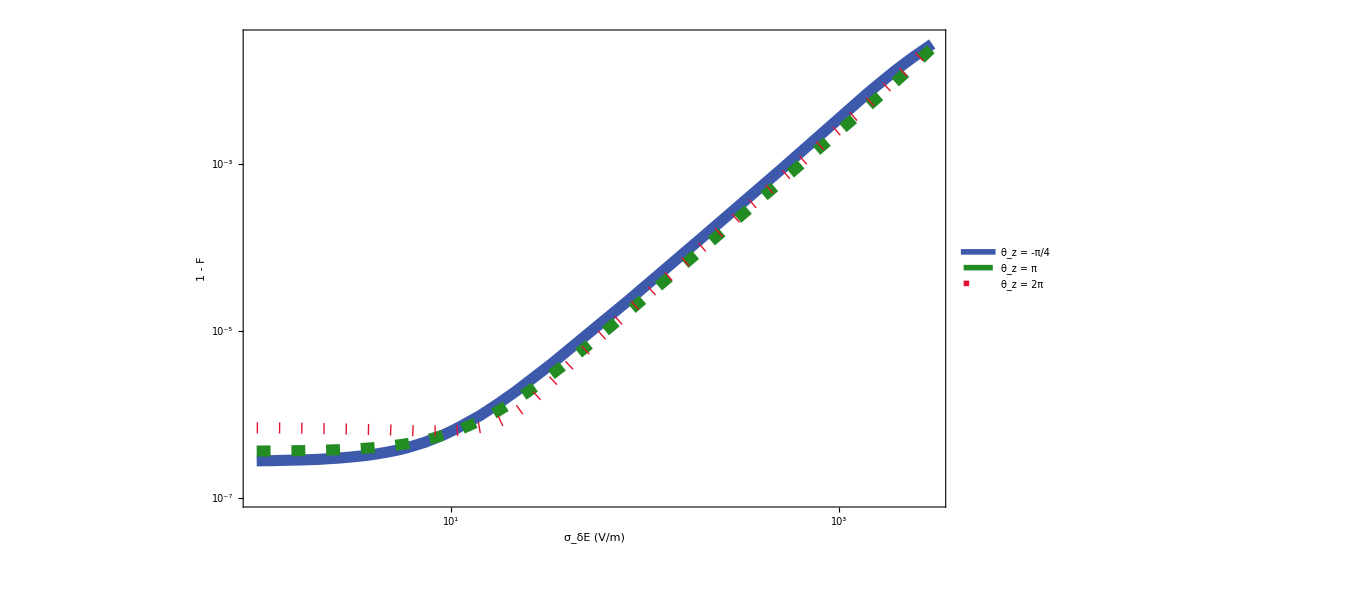

ZnoisePlotLogLog.eps

```mathematica
(* GENERATE zPhase PLOT *)
maxX = 3000;
xTicks = LinTicks[0, 2*maxX, 50, 5, TickLengthScale->2,TickLabelStep->1];
xxTicks = LinTicks[0, 2*maxX, 50, 5, TickLengthScale->2,TickLabelStep->1, ShowTickLabels->False];
yTicks = LogTicks[10,-15,10,TickLabelStep->1,TickLengthScale->2,ShowMinorTicks->True];
yyTicks = LogTicks[10,-15,10,ShowTickLabels->False,TickLengthScale->2,ShowMinorTicks->True];

labelFontSize = 45;
legendFontSize = 45;
xLabel = "σ_δE (V/m)";
yLabel = "1 - F";
curveThickness = 8;
curveOpacity = .5;

(* create legend *)
legend = Placed[{
Style["ϕ_z = π/4",legendFontSize],
Style["ϕ_z = π",legendFontSize],
Style["ϕ_z = 2π",legendFontSize]
},{{.7, .3}, {0, 0}}];
legendLog = Placed[{
Style["θ_z = -π/4",legendFontSize],
Style["θ_z = π",legendFontSize],
Style["θ_z = 2π",legendFontSize]
},{{.15, .55}, {0, 0}}];

xRange = {10^-3, maxX};
xRangeLog = {10^-0 // Log10, maxX // Log10};
yRangeLog = {10^-7 // Log10, 10^-1.5 // Log10};

(*Show[
Plot[{
1 - MeanGivenSD[σ, 0, RzFidelityFunctions[[1]]] // Log10,
1 - MeanGivenSD[σ, 0, RzFidelityFunctions[[2]]] // Log10,
1 - MeanGivenSD[σ, 0, RzFidelityFunctions[[3]]] // Log10
},
 {σ,xRange[[1]], xRange[[2]]},
PlotRange->{xRange, yRange},LabelStyle->{FontFamily-> "Times"},
PlotStyle->{
{AbsoluteThickness[curveThickness],Cobalt},
{AbsoluteThickness[curveThickness],ForestGreen},
{AbsoluteThickness[curveThickness],GeraniumLake}
},
PlotLegends->legend,Axes->False,
PlotPoints->10,
MaxRecursion->3
],
LabelStyle->{FontFamily-> "Times"},ImageSize->{1000, 1000},AspectRatio->.6,
FrameStyle->Directive[Thick,labelFontSize,Black],Frame->True,
FrameLabel->{Style[xLabel,labelFontSize],Style[yLabel,labelFontSize]},
FrameTicks->{xTicks,yTicks,xxTicks,yyTicks}
]
Export["ZnoisePlot.eps", %]*)

Show[
Plot[{
1 - MeanGivenSD[10^σ, 0, RzFidelityFunctions[[1]]] // Log10,
1 - MeanGivenSD[10^σ, 0, RzFidelityFunctions[[2]]] // Log10,
1 - MeanGivenSD[10^σ, 0, RzFidelityFunctions[[3]]] // Log10
},
 {σ,xRangeLog[[1]], xRangeLog[[2]]},
PlotRange->{xRangeLog, yRangeLog},LabelStyle->{FontFamily-> "Times"},
PlotStyle->{
{AbsoluteThickness[curveThickness],Cobalt},
{AbsoluteThickness[curveThickness],ForestGreen, AbsoluteDashing[{10, 15}]},
{AbsoluteThickness[curveThickness],GeraniumLake, AbsoluteDashing[{1, 15}]}
},
PlotLegends->legendLog,Axes->False,
PlotPoints->10,
MaxRecursion->3
],
LabelStyle->{FontFamily-> "Times"},ImageSize->{1000, 1000},AspectRatio->.6,
FrameStyle->Directive[Thick,labelFontSize,Black],Frame->True,
FrameLabel->{Style[xLabel,labelFontSize],Style[yLabel,labelFontSize]},
FrameTicks->{yTicks,yTicks,yyTicks,yyTicks}
]
Export["ZnoisePlotLogLog.eps", %]
```